# Practical 3 Rahul Chopra | BSc(H) Computer Science | Sem - IV | 20211449 Newton Raphson Method

## Question 1 :

x0=1.5

Nmax=20

epsilon=1/1000000

f[x]:=Cos[x]

f'[x]:=-Sin[x]

In 1th number of iterations the root is:1.57091

Estimated error is:0.0709148

In 2th number of iterations the root is:1.5708

Estimated error is:0.000118518

Return[1.5708]

The final approximation of root is:1.5708

Estimated error is:5.54889×10^-13

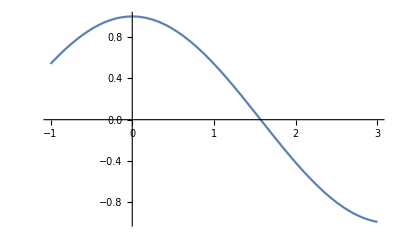

```mathematica
x0=Input["Enter first guess:"];
Nmax=Input["Enter maximum number of iterations:"];
eps=Input["Enter the value of convergence parameter:"];
Print["x0=",x0];
Print["Nmax=",Nmax];
Print["epsilon=",eps];
f[x_]:=Cos[x];
Print["f[x]:=",f[x]];
Print["f'[x]:=",D[f[x],x]];
For[i=1,i≤Nmax,i++,x1=N[x0-(f[x]/. x->x0)/(D[f[x],x]/. x->x0)];
If[Abs[x1-x0]<eps,Return[x1],x0p=x0;x0=x1;];
Print["In ",i,"th number of iterations the root is:",x1];
Print["Estimated error is:",Abs[x1-x0p]]];
Print["The final approximation of root is:",x1];
Print["Estimated error is:",Abs[x1-x0]];
Plot[f[x],{x,-1,3}]
```

## Question 2 :

x0=1.5

Nmax=20

epsilon=1/1000000

f[x]:=1-5 x+x^3

f'[x]:=-5+3 x^2

In 1th number of iterations the root is:3.28571

Estimated error is:1.78571

In 2th number of iterations the root is:2.55386

Estimated error is:0.73185

In 3th number of iterations the root is:2.21833

Estimated error is:0.33553

In 4th number of iterations the root is:2.13386

Estimated error is:0.0844789

In 5th number of iterations the root is:2.12844

Estimated error is:0.00541474

In 6th number of iterations the root is:2.12842

Estimated error is:0.0000218294

Return[2.12842]

The final approximation of root is:2.12842

Estimated error is:3.54197×10^-10

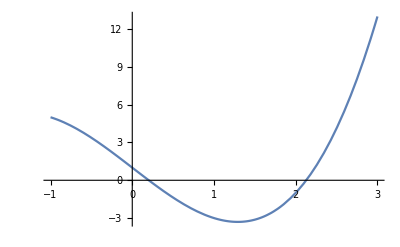

```mathematica
x0=Input["Enter first guess:"];
Nmax=Input["Enter maximum number of iterations:"];
eps=Input["Enter the value of convergence parameter:"];
Print["x0=",x0];
Print["Nmax=",Nmax];
Print["epsilon=",eps];
f[x_]:=x^3-5x+1;
Print["f[x]:=",f[x]];
Print["f'[x]:=",D[f[x],x]];
For[i=1,i≤Nmax,i++,x1=N[x0-(f[x]/. x->x0)/(D[f[x],x]/. x->x0)];
If[Abs[x1-x0]<eps,Return[x1],x0p=x0;x0=x1;];
Print["In ",i,"th number of iterations the root is:",x1];
Print["Estimated error is:",Abs[x1-x0p]]];
Print["The final approximation of root is:",x1];
Print["Estimated error is:",Abs[x1-x0]];
Plot[f[x],{x,-1,3}]
```

## Question 3 :

x0=1.5

Nmax=20

epsilon=1/1000000

f[x]:=-ⅇ^x x+Cos[x]

f'[x]:=-ⅇ^x-ⅇ^x x-Sin[x]

In 1th number of iterations the root is:0.954848

Estimated error is:0.545152

In 2th number of iterations the root is:0.632019

Estimated error is:0.322829

In 3th number of iterations the root is:0.527616

Estimated error is:0.104403

In 4th number of iterations the root is:0.517838

Estimated error is:0.00977784

In 5th number of iterations the root is:0.517757

Estimated error is:0.0000806043

Return[0.517757]

The final approximation of root is:0.517757

Estimated error is:5.44033×10^-9

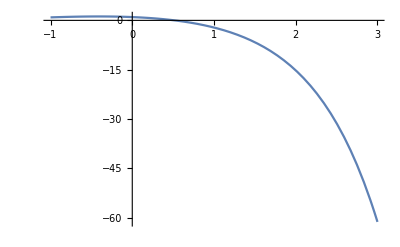

```mathematica
x0=Input["Enter first guess:"];
Nmax=Input["Enter maximum number of iterations:"];
eps=Input["Enter the value of convergence parameter:"];
Print["x0=",x0];
Print["Nmax=",Nmax];
Print["epsilon=",eps];
f[x_]:=Cos[x]-x*Exp[x];
Print["f[x]:=",f[x]];
Print["f'[x]:=",D[f[x],x]];
For[i=1,i≤Nmax,i++,x1=N[x0-(f[x]/. x->x0)/(D[f[x],x]/. x->x0)];
If[Abs[x1-x0]<eps,Return[x1],x0p=x0;x0=x1;];
Print["In ",i,"th number of iterations the root is:",x1];
Print["Estimated error is:",Abs[x1-x0p]]];
Print["The final approximation of root is:",x1];
Print["Estimated error is:",Abs[x1-x0]];
Plot[f[x],{x,-1,3}]
```